## Troy’s consistent marginals - with fixed noise

```mathematica
sigma=0.8;
n=100000;
muSamples=RandomVariate[UniformDistribution[{-3,3}],n];
q=ParallelTable[RandomVariate[NormalDistribution[muSamples[[i]],sigma],{1}][[1]],{i,1,Length@muSamples,1}];
data=ParallelTable[PDF[NormalDistribution[0,1],q[[i]]],{i,1,Length@q,1}];
```

```mathematica
dens=SmoothKernelDistribution[q];
pfprior=Table[PDF[dens,q[[i]]],{i,1,Length@q,1}];
ratio=data/pfprior;
```

```mathematica
lnormrat=ratio/Max[ratio];
```

```mathematica
muKept=Table[If[lnormrat[[i]]>RandomReal[],{q[[i]],muSamples[[i]]},-1],{i,1,Length@lnormrat}];
```

```mathematica
muFinal=DeleteCases[muKept,-1];
```

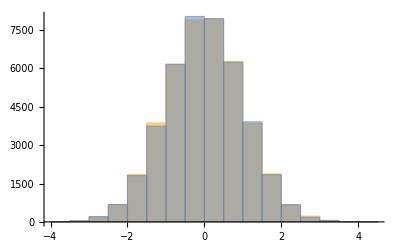

```mathematica
Histogram[{muFinal[[All,1]],RandomVariate[NormalDistribution[0,1],{Length@muFinal}]}]
```

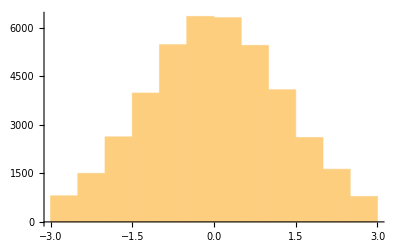

```mathematica
Histogram[muFinal[[All,2]]]
```

```mathematica
qTest=ParallelTable[RandomVariate[NormalDistribution[muFinal[[All,2]][[i]],0.8],{1}][[1]],{i,1,Length@muFinal[[All,2]],1}];
```

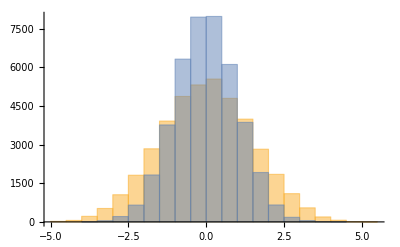

```mathematica
Histogram[{qTest,RandomVariate[NormalDistribution[0,1],{Length@qTest}]}]
```